# Mathematica 101

## Some simple computations ...

You can use Mathematica as a calculator (use Shift + Enter to evaluate a cell)

```mathematica
1+1
```

2

You can assign results to variables for later use

```mathematica
var=1+1
```

2

```mathematica
var^3
```

8

Mathematica data structures are mostly list based

```mathematica
list={1,2,3,4,5}
```

{1,2,3,4,5}

Most mathematical operators can be used on lists directly

```mathematica
list/3
```

{1/3,2/3,1,4/3,5/3}

Even matrices are implemented as lists of lists

```mathematica
matrix={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

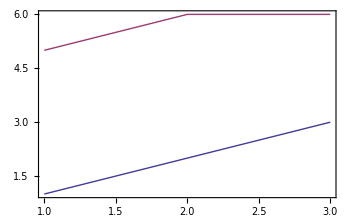

```mathematica
ListPlot[{{1,2,3},{5,6,6}},Joined->True]
```

```mathematica
Eigenvalues[{{1,2,3},{4,5,6},{7,8,9}}]
```

{3/2 (5+√33),3/2 (5-√33),0}

Formatting functions can be used to make data structures more readable

```mathematica
MatrixForm[matrix]
TableForm[matrix]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9

```mathematica
MatrixRank[matrix]
```

2

You can do many things with lists. First, let’s generate a list programmatically

```mathematica
list=Range[1,9]
```

{1,2,3,4,5,6,7,8,9}

Let’s partition the list to regenerate the matrix from the previous example

```mathematica
matrix=Partition[list,3]
MatrixForm[matrix]
```

{{1,2,3},{4,5,6},{7,8,9}}

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

We can flatten the matrix to obtain the original list

```mathematica
Flatten[matrix]
```

{1,2,3,4,5,6,7,8,9}

We can access certain parts of the list or the matrix using the [[]] (Part) operator

```mathematica
list[[2]]
list[[-2]]
list[[2;;-2]]
```

2

8

{2,3,4,5,6,7,8}

```mathematica
matrix[[2(*rows*),3(*columns*)]]
matrix[[1;;2(*rows*),3(*columns*)]]
```

6

{3,6}

```mathematica
list
```

{1,2,3,4,5,6,7,8,9}

```mathematica
reverseList=Reverse[list]
```

{9,8,7,6,5,4,3,2,1}

Combining data is easy

```mathematica
Thread[{list,reverseList}]
Thread[list->reverseList]
```

{{1,9},{2,8},{3,7},{4,6},{5,5},{6,4},{7,3},{8,2},{9,1}}

{1→9,2→8,3→7,4→6,5→5,6→4,7→3,8→2,9→1}

## Everything is an expression ...

### Many expressions are rendered and entered using special syntax and notation. However, internally they look all the same (head[args...]). This can be made visible using the Function FullForm. In this way Mathematica is very similar to functional programming languages like Lisp, Scheme etc, e.g., (operator arg1 arg2 arg3 ...) -> (+ 1 2 3).

```mathematica
{1,2,3}
1->3
1/3
```

{1,2,3}

1→3

1/3

```mathematica
FullForm[{1,2,3}]
FullForm[1->3]
FullForm[1/3]
```

List[1,2,3]

Rule[1,3]

Rational[1,3]

### Use Head to get the head of an expression

```mathematica
Head[{1,2,3}]
Head[3.]
Head[1/2]
```

List

Real

Rational

### Changing the Head of a function using Apply (@@)

```mathematica
NewHead@@{1,2,3}
Apply[NewHead,{1,2,3}]
```

NewHead[1,2,3]

NewHead[1,2,3]

```mathematica
Plus@@{1,2,3}
Times@@{1,2,3}
```

6

6

## Mathematica caveats and how to avoid them

### You have to be aware of the fact that the order of evaluation is not preserved in a Notebook environment. That is a cool feature in a prototyping setting but can lead to non-trivial errors, responsible for most of the voodoo going on

```mathematica
a=1;
b=2;
```

```mathematica
a/b
```

1/2

```mathematica
b=0
```

0

### Quiting the kernel (using either the menu, Evaluation -> Quit Kernel or the function Quit[]) helps resolving those issues. Encapsulating code into functions and avoiding lots of variables assignments helps too.

```mathematica
Quit[]
```

```mathematica
a=1
```

1

```mathematica
a
```

1

```mathematica
a=1
```

1

```mathematica
a="string"
```

string

```mathematica
a
```

string

### Previous definitions of a variable can be erased using Clear[var1, ...]

```mathematica
a=1
```

1

```mathematica
a
```

1

```mathematica
a
```

a

```mathematica
Clear[a]
```

```mathematica
a
```

a

## Mathematica patterns and rule-based programming

### What are patterns (patternID_Head)? Think of them as some kind of ‘regular expressions’ but for all kinds of expressions.

### A _ represents a pattern and matches any expression

```mathematica
_
```

```mathematica
MatchQ[1,_String]
MatchQ[1.,_String]
MatchQ["one",_String]
```

False

False

True

```mathematica
MatchQ["one",_String]
```

```mathematica
#->MatchQ[#,_]&/@{1,1.,"String",1/3,{1,2,3,4}}
```

{1→True,1.→True,String→True,1/3→True,{1,2,3,4}→True}

### How to construct a pattern (_) that matches only certain expressions?

```mathematica
#->MatchQ[#,_String]&/@{1,1.,"String",1/3,{1,2,3,4}}
```

{1→False,1.→False,String→True,1/3→False,{1,2,3,4}→False}

```mathematica
#->MatchQ[#,_Rational]&/@{1,1.,"String",1/3,{1,2,3,4}}
```

{1→False,1.→False,String→False,1/3→True,{1,2,3,4}→False}

### Conditional patterns (pattern_ /; Condition[pattern] )

```mathematica
Head[4.]
```

Real

```mathematica
Cases[{{1,2,3,4.},{1,2,3}},l_List/;Length[l]≥4&&MemberQ[l,88.]]
```

{}

### Matching a sequence of expressions

#### Matching a bunch of Integers in a list

```mathematica
MatchQ[{1,2,3,4},{__Integer}]
```

#### They have to be all integers

```mathematica
MatchQ[{1,2,3,4.},{__Integer}]
```

#### There has to be at least on integer present

```mathematica
MatchQ[{},{__Integer}]
```

#### ___Integer matches 0 or more integers

```mathematica
MatchQ[{},{___Integer}]
```

### Some neat functions that utilize patterns

```mathematica
Cases[{1,2,3,4.},_Real]
```

{4.}

```mathematica
Count[{1,2,3,4.},_Real]
```

1

```mathematica
Cases[{{1,2,3,4.}},_Real]
```

{}

```mathematica
Cases[{{1,2,3,4.}},_Real,Infinity]
```

{4.}

### Rule-based programming

```mathematica
{1,2,3,4.}/.i_Real/;i>2:>i^2
```

{1,2,3,16.}

```mathematica
FullForm[Hold[{1,2,3,4}/.i_/;i>2:>i^2]]
```

Hold[ReplaceAll[List[1,2,3,4],RuleDelayed[Condition[Pattern[i,Blank[]],Greater[i,2]],Power[i,2]]]]

## Defining functions

### Divide & Conquer: Encapsulate your stuff into Mathematica functions.

Always ...
1. Localize all local variables (using Module)!
2. Never, ever, use global variables!
3. Use strongly typed arguments and check user input (which is pretty easy as patterns are used to specify arguments)!
4. Abort evaluation (and provide a meaningful message) if user input does not match the function’s argument signature

```mathematica
Unprotect[function];
function::wrngargs="Provided arguments don't match any definition of function";
function[arg1_Integer,arg2_List]:=Module[{localVariable},
localVariable=arg1+2;
localVariable+arg2
];
function[arg1_Real,arg2_List]:=Module[{localVariable},
localVariable=arg1+2;
localVariable/arg2
];
function[___]:=(Message[function::wrngargs];Abort[])
Protect[function];
```

```mathematica
function[1,{1,2,3}]
```

{4,5,6}

```mathematica
function[1.,{1,2,3}]
function[1.]
function[1,{1,2,3},3.]
```

{3.,1.5,1.}

function::wrngargs: Provided arguments don't match any definition of function

$Aborted

function::wrngargs: Provided arguments don't match any definition of function

$Aborted

```mathematica
function=1
```

Set::wrsym: Symbol function is Protected.

1

### Lambda functions (λ calculus; anonymous functions; good for quick hacks ...)

#### The slot symbol # represents an argument

```mathematica
#&[2]
```

2

```mathematica
#^2&[2]
```

4

#### #2 represents the second argument provided

```mathematica
#1^#2&[2,3]
```

8

### Applying functions to expressions ...

#### Map (/@)

```mathematica
#[[1]],#[[2]]]&/@{{1,{1,2,3}},{2,{2,3,4}}}
function[#[[1]],#[[2]]]&/@{{1.,{1,2,3}},{2.,{2,3,4}}}
```

## General tips

### Use the documentation system (Context menu -> Get Help)

```mathematica
NDSolve
```

### Keyboard shortcuts

Cmd + Alt + ]

Cmd + Alt + Shift + }

### Avoid writing C code in Mathematica. Use rule-based programming, functional programming, constructs like Map, Apply, etc., lambda functions ...

```mathematica
stuff={};
For[i=0,i<4,i++,
AppendTo[stuff,i]
];
```

```mathematica
stuff=Table[i,{i,0,3}]
```

{0,1,2,3}

### Use only lowercase variable and function names (uppercase is reserved for Mathematica built-ins)

### Many Mathematica functions allow for flexibility by providing Options. A set of default options is used if the user is not specific. For example, many plotting functions work in that way.

#### Look up a function’s set of available options

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

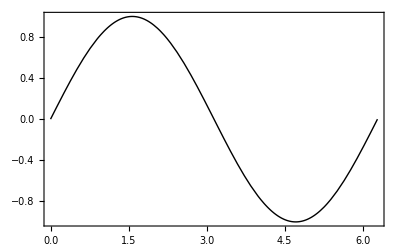

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle->Black,Frame->True,Axes->False]
```

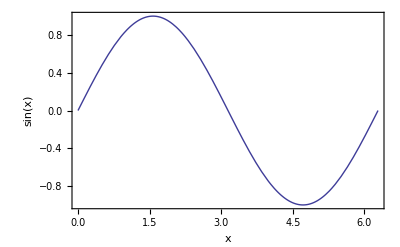

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,FrameLabel->{"x","sin(x)"}]
```

#### You can change the options of a functions globally. This helps a lot in avoiding redundant code

```mathematica
SetOptions[Plot,Frame->True,LabelStyle->{FontSize->12,FontFamily->"Helvetica"}];
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,FrameLabel->{"x","sin(x)"}]
```

-Graphics-

### Using Mathematica’s dynamic capabilities to see how results change with varying parameters

```mathematica
Manipulate[
Plot[Sin[x*freq+phase],{x,0,2Pi},Frame->True,FrameLabel->{"x","sin(x)"},ImageSize->300,PlotRange->{All,{-2,2}}],{freq,1,10},{phase,0,2π}]
```

### Check out http://demonstrations.wolfram.com/ for more examples

### Parallelize computations by using ParallelTable, ParallelDo etc.

```mathematica
AbsoluteTiming[
Table[
Eigenvalues[RandomReal[{0,1},{100,100}]]
,{100}
];
]
```

{1.26719,Null}

```mathematica
AbsoluteTiming[
ParallelTable[
Eigenvalues[RandomReal[{0,1},{100,100}]]
,{100}
];
]
```

{0.692283,Null}

## More resources

Best resource and tutorial collection ever